```mathematica
Head[2+3I]
```

Complex

```mathematica
Random[Complex]
```

0.501532+0.940668 ⅈ

```mathematica
Random[Complex,{-1-I,1+I}]
```

-0.217901-0.311196 ⅈ

```mathematica
Random[Real,{-1,1}] + I Random[Real,{-1,1}]
```

-0.446098-0.71068 ⅈ

```mathematica
Table[a[i],{5}]
```

{a[i],a[i],a[i],a[i],a[i]}

```mathematica
Table[a[i],{5},{5}]//MatrixForm
```

(a[i] | a[i] | a[i] | a[i] | a[i]
a[i] | a[i] | a[i] | a[i] | a[i]
a[i] | a[i] | a[i] | a[i] | a[i]
a[i] | a[i] | a[i] | a[i] | a[i]
a[i] | a[i] | a[i] | a[i] | a[i])

```mathematica
(*-------------------*)
```

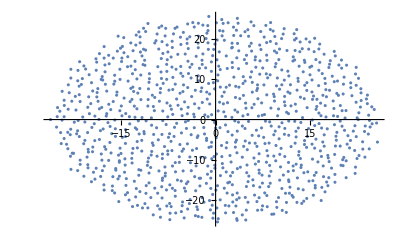

-Graphics-

```mathematica
MRand[n_,m_]=Table[ Random[Complex,{-1-I,1+I}],{n},{m}];

eig = Eigenvalues[MRand[1000,1000]];

punti= Table[ 
                          x=Re[eig[[i]]];
		        y=Im[eig[[i]]];
{x,y}, 
{i,1,Length[eig]}
];

punti2= Map[ (  {Re[#],Im[#]} ) &, eig];

ListPlot[punti]
ListPlot[punti2]
```

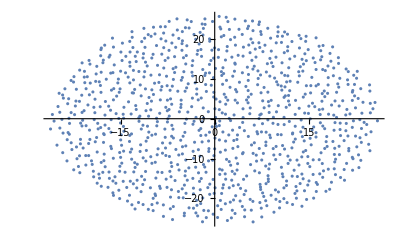

```mathematica
ListPlot[(Tooltip[{Re[#1],Im[#1]}]&)/@eig]
```

```mathematica
(*-------------------------*)
```

```mathematica
sequenza[c_]:= Module [ {risultato},
		   z[0]=0;

          Do[     z[i]=z[i-1]^2 +c;
         risultato =i;
  If[ Abs[ z[i] ]>2,
       Break[]
            ],

         {i,1,100}
           ];

risultato
                                                ];

mandelbrot = ContourPlot[ punto = sequenza[x+I y];
						punto,
			{x,-0.6,-0.4},{y,0.4,0.6}, PlotPoints->200]
```

-Graphics-